Import the graph and get the pruned network and partition

```mathematica
AppendTo[$Path, FileNameJoin[{$HomeDirectory,"network-similarity"}]];
g = Import["subject_tagged_network.gml"];
```

```mathematica
Show[g]
```

```mathematica
parents = Position[VertexOutDegree[g], _?(#>0&)] // Flatten;
popular = Position[VertexInDegree[g], _?(#>1&)] // Flatten;
pruned= Subgraph[g, Union[parents, popular],Options[g],VertexSize->Large];
prunedU = UndirectedGraph[pruned, Options[pruned]];
prunedCC =Subgraph[pruned,WeaklyConnectedComponents[pruned][[1]],Options[pruned],ImageSize->Full];
partition = FindGraphPartition[prunedCC];
communities = FindGraphCommunities[prunedCC];
```

```mathematica
PropertyList[{g,1}]
```

{citationCount,isBio,isBioMath,isCS,isCSBio,isCSMath,isMath,referenceCount,subject,title,toRead,year,VertexCoordinates,VertexShape,VertexShapeFunction,VertexSize,VertexStyle}

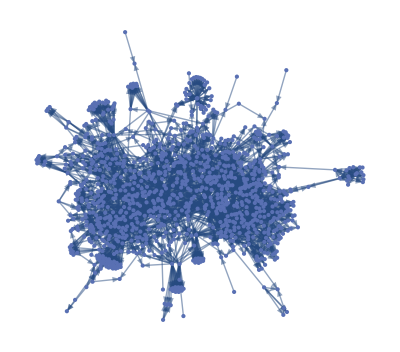

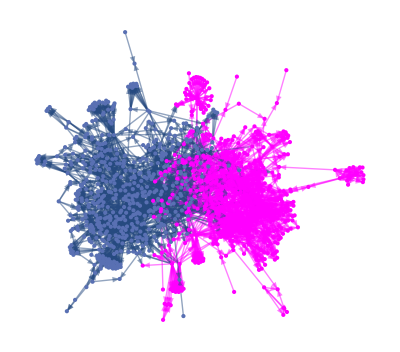

```mathematica
Show[prunedCC]
Show[HighlightGraph[prunedCC,Style[side1,RGBColor["Fuchsia"]]]]
```

Get the assortativities by various subject properties

NOTE: “isCSBio”, etc., are “either CS OR bio”

```mathematica
side1 =  Subgraph[g,partition[[1]],Options[g],VertexSize->Large];
side2 = Subgraph[g,partition[[2]],Options[g],VertexSize->Large];
testGraphs = {g,prunedCC,side1,side2};
properties = {"year","citationCount","referenceCount","subject","isCS","isBio","isMath","isCSBio","isCSMath","isBioMath"};
assortativities = {{"","g","prunedCC","side 1","side 2"}};

row1 = {"outdegree"};
For[j=1,j≤Length[testGraphs],j++,AppendTo[row1,NumberForm[GraphAssortativity[testGraphs[[j]]]//N,{5,4}]]]
AppendTo[assortativities,row1];
For[i=1,i≤Length[properties],i++,
p= properties[[i]];
row = {p};
For[j=1,j≤Length[testGraphs],j++,
AppendTo[row,NumberForm[ GraphAssortativity[testGraphs[[j]],p]//N,{5,4}]];
];
AppendTo[assortativities,row];
]
Grid[assortativities,Alignment->Right]
```

| g | prunedCC | side 1 | side 2
outdegree | -0.0178 | -0.0141 | 0.0177 | -0.0461
year | 0.0067 | 0.0041 | -0.0054 | 0.0108
citationCount | 0.0006 | 0.0654 | 0.1020 | -0.0649
referenceCount | 0.0193 | -0.0061 | -0.0097 | -0.0019
subject | 0.1920 | 0.0795 | 0.0399 | -0.0370
isCS | 0.2642 | 0.1549 | 0.0936 | -0.0566
isBio | 0.3370 | 0.1815 | 0.1200 | -0.0222
isMath | 0.0825 | 0.0125 | -0.0027 | 0.0029
isCSBio | 0.1530 | 0.0235 | 0.0132 | -0.0565
isCSMath | 0.2464 | 0.1262 | 0.0665 | -0.0578
isBioMath | 0.1890 | 0.0532 | 0.0272 | -0.0411

```mathematica
undirectedAssortativities = {{"","g","prunedCC","side 1","side 2"}};
undirectedTestGraphs = {};
For[i=1,i≤Length[testGraphs],i++,
AppendTo[undirectedTestGraphs,UndirectedGraph[testGraphs[[i]],Options[testGraphs[[i]]]]];
]
For[i=1,i≤Length[properties],i++,
p= properties[[i]];
row = {p};
For[j=1,j≤Length[testGraphs],j++,
AppendTo[row, GraphAssortativity[undirectedTestGraphs[[j]],p]//N];
];
AppendTo[undirectedAssortativities,row];
]
Grid[undirectedAssortativities,Alignment->Left]
```

| g | prunedCC | side 1 | side 2
year | -0.00813322 | -0.0101044 | -0.0268819 | -0.00444279
citationCount | -0.00554084 | -0.0178149 | -0.0122597 | -0.0331821
referenceCount | 0.00538945 | -0.0674486 | -0.0572942 | -0.0911446
subject | 0.181402 | 0.0708897 | 0.0534282 | -0.0652706
isCS | 0.262276 | 0.152812 | 0.124786 | -0.0755055
isBio | 0.333259 | 0.177251 | 0.118302 | -0.0208978
isMath | 0.0648037 | 0.016036 | 0.0221645 | -0.00281899
isCSBio | 0.149456 | 0.0188095 | 0.0251762 | -0.0768234
isCSMath | 0.24375 | 0.12547 | 0.0966304 | -0.0902675
isBioMath | 0.163222 | 0.0413886 | 0.027722 | -0.0292626

Get the list of vertex IDs on the to-read list

```mathematica
vertices = {};
For[i=1,i≤VertexCount[g],i++,
If[PropertyValue[{g,i},"toRead"]==1.,AppendTo[vertices,i]]]
vertices
```

{1,5,7,10,14,28,39,44,46,50,54,55,58,78,97,98,103,104,105,109,117,123,128,193,262,315,317,318,326,349,365,368,369,611,745,755,857,861,888,1199,1310,1320,1416,2015,2140,2432,2577,2593,2631,3025,3158,3181,3230,3398,4094,4217,4655,4679,4962,5345,5765}

```mathematica
VertexOutDegree[prunedCC,50]
PropertyValue[{prunedCC,50},"title"]
```

0

Biological network comparison using graphlet degree distribution

```mathematica
Length[vertices]
```

61

```mathematica
For[i=1,i≤Length[vertices],i++,
Print[vertices[[i]], " ", PropertyValue[{g,vertices[[i]]},"title"]]]
```

1 Fifty years of graph matching, network alignment and network comparison

5 Networks for systems biology: conceptual connection of data and function

7 Global network alignment using multiscale spectral signatures

10 Error correcting graph matching: on the influence of the underlying cost function

14 MAGNA: Maximizing Accuracy in Global Network Alignment

28 Graphlet-based measures are suitable for biological network comparison

39 On Graph Kernels: Hardness Results and Efficient Alternatives

44 Pairwise Alignment of Protein Interaction Networks

46 Alignment-free protein interaction network comparison

50 Biological network comparison using graphlet degree distribution

54 NETAL: a new graph-based method for global alignment of protein\u2013protein interaction networks

55 Computers and Intractability: A Guide to the Theory of NP-Completeness (Michael R. Garey and David S. Johnson)

58 Recent developments in graph matching

78 Modeling cellular machinery through biological network comparison

97 A graph distance metric based on the maximal common subgraph

98 THIRTY YEARS OF GRAPH MATCHING IN PATTERN RECOGNITION

103 Collective dynamics of \u2018small-world\u2019 networks

104 A new graph-based method for pairwise global network alignment

105 An Algorithm for Subgraph Isomorphism

109 On a relation between graph edit distance and maximum common subgraph

117 Topological network alignment uncovers biological function and phylogeny

123 A linear programming approach for the weighted graph matching problem

128 An eigendecomposition approach to weighted graph matching problems

193 A graduated assignment algorithm for graph matching

262 A new algorithm for subgraph optimal isomorphism

315 A distance measure between attributed relational graphs for pattern recognition

317 Inexact graph matching for structural pattern recognition

318 A new algorithm for error-tolerant subgraph isomorphism detection

326 Structural Descriptions and Inexact Matching

349 A shape analysis model with applications to a character recognition system

365 A graph distance measure for image analysis

368 Structural matching in computer vision using probabilistic relaxation

369 Hierarchical attributed graph representation and recognition of handwritten chinese characters

611 Linear time algorithm for isomorphism of planar graphs (Preliminary Report)

745 Pairwise Global Alignment of Protein Interaction Networks by Matching Neighborhood Topology

755 Conserved patterns of protein interaction in multiple species

857 Approximate graph edit distance computation by means of bipartite graph matching

861 Local graph alignment and motif search in biological networks

888 Network Motifs: Simple Building Blocks of Complex Networks

1199 The Hungarian method for the assignment problem

1310 Graph Matching Based on Node Signatures

1320 Exact and approximate graph matching using random walks

1416 Global alignment of multiple protein interaction networks with application to functional orthology detection

2015 Fast parallel algorithms for graph similarity and matching

2140 Fast computation of Bipartite graph matching

2432 Fast and Scalable Approximate Spectral Matching for Higher Order Graph Matching

2577 A Probabilistic Approach to Spectral Graph Matching

2593 Graph matching applications in pattern recognition and image processing

2631 The graph matching problem

3025 Graph-based methods for analysing networks in cell biology

3158 BIG-ALIGN: Fast Bipartite Graph Alignment

3181 A (sub)graph isomorphism algorithm for matching large graphs

3230 Complex network measures of brain connectivity: Uses and interpretations

3398 Efficient Graph Similarity Search Over Large Graph Databases

4094 Demadroid: Object Reference Graph-Based Malware Detection in Android

4217 Indian sign language recognition using graph matching on 3D motion captured signs

4655 Predicting Graph Categories from Structural Properties

4679 Survey on the Graph Alignment Problem and a Benchmark of Suitable Algorithms

4962 Efficient Graph Matching Algorithms

5345 Early Estimation Model for 3D\u2013Discrete Indian Sign Language Recognition Using Graph Matching

5765 Unsupervised Domain Adaptation Using Regularized Hyper-Graph Matching

Get the list of vertices of each subject classification and count up the intersections with partition members

```mathematica
isCS = {};isBio = {}; isMath={};
For[i=1,i≤VertexCount[g],i++,
If[PropertyValue[{g,i},"isCS"]==1.0,AppendTo[isCS,i]];
If[PropertyValue[{g,i},"isBio"]==1.0,AppendTo[isBio,i]];
If[PropertyValue[{g,i},"isMath"]==1.0,AppendTo[isMath,i]];
]
```

```mathematica
numSubjects = {{"","g","prunedCC","gsub","gsub-1","gsub-2","side 1","side 2"}};
tagged = Union[isBio,isMath,isCS];
untagged = Complement[VertexList[g],tagged];
subjLists = {VertexList[g],tagged, untagged,isCS,isBio,isMath,Intersection[isCS,isBio],Intersection[isCS,isMath],Intersection[isBio,isMath],Intersection[isBio,isCS,isMath]};
subjNames = {"all","tagged", "untagged","isCS","isBio","isMath","bothCSBio","bothCSMath","bothBioMath","all three"};
vertLists = {VertexList[g],VertexList[prunedCC],vertices,Intersection[vertices,partition[[1]]],Intersection[vertices,partition[[2]]],partition[[1]],partition[[2]]};
For[i=1,i≤Length[subjLists],i++,
counts = {subjNames[[i]]};
For[j=1,j≤Length[vertLists],j++,
AppendTo[counts,Length[Intersection[vertLists[[j]],subjLists[[i]]]]]
];
AppendTo[numSubjects,counts];
]
Grid[numSubjects,Alignment->Left]
```

| g | prunedCC | gsub | gsub-1 | gsub-2 | side 1 | side 2
all | 5793 | 1062 | 61 | 27 | 34 | 531 | 531
tagged | 3871 | 560 | 30 | 8 | 22 | 220 | 340
untagged | 1922 | 502 | 31 | 19 | 12 | 311 | 191
isCS | 2533 | 405 | 24 | 2 | 22 | 93 | 312
isBio | 984 | 122 | 6 | 6 | 0 | 108 | 14
isMath | 787 | 97 | 3 | 1 | 2 | 44 | 53
bothCSBio | 108 | 13 | 1 | 1 | 0 | 9 | 4
bothCSMath | 305 | 49 | 2 | 0 | 2 | 15 | 34
bothBioMath | 24 | 3 | 0 | 0 | 0 | 2 | 1
all three | 4 | 1 | 0 | 0 | 0 | 1 | 0

```mathematica
GraphAssortativity[g,{tagged,untagged}]//N
pverts = VertexList[prunedCC];
GraphAssortativity[prunedCC,{Intersection[tagged,pverts],Intersection[untagged,pverts]}]//N
```

0.108968

-0.0094113

Check on that with the modularity communities, too (useless)

```mathematica
headers = {{"size","side1","side2","side1-isCS","side1-isBio","side2-isCS","side2-isBio"}};
wrongsideCS = 0;
rightsideCS = 0;
wrongsideBio = 0;
rightsideBio=0;
For[i=1,i≤Length[communities],i++,
c = communities[[i]];
cSide1 = Intersection[partition[[1]],c];
cSide2 = Intersection[partition[[2]],c];
c1CS = Length[Intersection[subjLists[[2]],cSide1]];
c1Bio =  Length[Intersection[subjLists[[3]],cSide1]];
c2CS =  Length[Intersection[subjLists[[2]],cSide2]];
c2Bio =  Length[Intersection[subjLists[[3]],cSide2]];
If[c1CS≥c2CS,wrongsideCS+=c2CS;rightsideCS+=c1CS];
If[c1CS<c2CS,wrongsideCS+=c1CS;rightsideCS+=c2CS];
If[c1Bio≥c2Bio,wrongsideBio+=c2Bio;rightsideBio+=c1Bio];
If[c1Bio<c2Bio,wrongsideBio+=c1Bio;rightsideBio+=c2Bio];
row = {Length[c],Length[cSide1],Length[cSide2],c1CS,c1Bio,c2CS,c2Bio};
AppendTo[headers,row];
]
Print[wrongsideCS,", ", rightsideCS,", ", wrongsideCS/rightsideCS//N];
Print[wrongsideBio,", ",rightsideBio,", ", wrongsideBio/rightsideBio//N];
Grid[headers,Alignment->Left]
```

48, 359, 0.133705

13, 109, 0.119266

size | side1 | side2 | side1-isCS | side1-isBio | side2-isCS | side2-isBio
253 | 11 | 242 | 7 | 4 | 175 | 4
180 | 162 | 18 | 11 | 57 | 6 | 1
162 | 150 | 12 | 25 | 19 | 3 | 2
109 | 9 | 100 | 2 | 2 | 52 | 3
81 | 18 | 63 | 5 | 1 | 25 | 2
77 | 50 | 27 | 15 | 2 | 14 | 2
65 | 52 | 13 | 15 | 0 | 7 | 0
32 | 2 | 30 | 1 | 0 | 20 | 1
30 | 30 | 0 | 14 | 1 | 0 | 0
28 | 21 | 7 | 3 | 9 | 3 | 0
20 | 20 | 0 | 0 | 9 | 0 | 0
19 | 6 | 13 | 2 | 2 | 0 | 1
6 | 0 | 6 | 0 | 0 | 2 | 0

Assign colors to vertices in the full list and toRead list (separately, because we want light colors for toRead)

```mathematica
toReadColors={};
For[i=1,i≤Length[vertices],i++,
If[PropertyValue[{g,vertices[[i]]},"subject"]=="0",AppendTo[toReadColors,vertices[[i]]->Directive[LightGray,EdgeForm[None]]]];
If[PropertyValue[{g,vertices[[i]]},"subject"]=="1",AppendTo[toReadColors,vertices[[i]]->Directive[LightRed,EdgeForm[None]]]];
If[PropertyValue[{g,vertices[[i]]},"subject"]=="2",AppendTo[toReadColors,vertices[[i]]->Directive[LightBlue,EdgeForm[None]]]];
If[PropertyValue[{g,vertices[[i]]},"subject"]=="3",AppendTo[toReadColors,vertices[[i]]->Directive[LightYellow,EdgeForm[None]]]];
If[PropertyValue[{g,vertices[[i]]},"subject"]=="12",AppendTo[toReadColors,vertices[[i]]->Directive[LightPurple,EdgeForm[None]]]];
If[PropertyValue[{g,vertices[[i]]},"subject"]=="13",AppendTo[toReadColors,vertices[[i]]->Directive[LightOrange,EdgeForm[None]]]];
If[PropertyValue[{g,vertices[[i]]},"subject"]=="23",AppendTo[toReadColors,vertices[[i]]->Directive[LightGreen,EdgeForm[None]]]];
If[PropertyValue[{g,vertices[[i]]},"subject"]=="123",AppendTo[toReadColors,vertices[[i]]->Directive[LightBrown,EdgeForm[None]]]];]
```

```mathematica
allColors={};
subVerts=VertexList[g];For[i=1,i≤Length[subVerts],i++,If[PropertyValue[{g,subVerts[[i]]},"subject"]=="0",AppendTo[allColors,subVerts[[i]]->Directive[LightGray,EdgeForm[None],PointSize[0.01]]]];
If[PropertyValue[{g,subVerts[[i]]},"subject"]=="1",AppendTo[allColors,subVerts[[i]]->Directive[Red,EdgeForm[None],PointSize[0.01]]]];
If[PropertyValue[{g,subVerts[[i]]},"subject"]=="2",AppendTo[allColors,subVerts[[i]]->Directive[Blue,EdgeForm[None],PointSize[0.01]]]];
If[PropertyValue[{g,subVerts[[i]]},"subject"]=="3",AppendTo[allColors,subVerts[[i]]->Directive[Yellow,EdgeForm[None],PointSize[0.01]]]];
If[PropertyValue[{g,subVerts[[i]]},"subject"]=="12",AppendTo[allColors,subVerts[[i]]->Directive[Purple,EdgeForm[None],PointSize[0.01]]]];
If[PropertyValue[{g,subVerts[[i]]},"subject"]=="13",AppendTo[allColors,subVerts[[i]]->Directive[Orange,EdgeForm[None],PointSize[0.01]]]];
If[PropertyValue[{g,subVerts[[i]]},"subject"]=="23",AppendTo[allColors,subVerts[[i]]->Directive[Green,EdgeForm[None],PointSize[0.01]]]];
If[PropertyValue[{g,subVerts[[i]]},"subject"]=="123",AppendTo[allColors,subVerts[[i]]->Directive[Brown,EdgeForm[None],PointSize[0.01]]]];]
```

```mathematica
colorkey = {{Framed["Key",ContentPadding->False,FrameStyle->Thin],SpanFromLeft},{Red,"Computer Science"},{Blue, "Biology"},{Yellow,"Mathematics"},{Orange,"CS + Math"},{Purple,"CS + Biology"},{Green,"Biology + Math"},{Brown,"CS + Math + Biology"},{LightGray,"No Subject Label"}};
Rasterize[Grid[colorkey,Alignment->Left],ImageResolution->300]
TableForm[colorkey]
GraphicsGrid[colorkey,AspectRatio->1.2,Alignment->Left]
```

-Graphics-

Key | 
RGBColor[1, 0, 0] | Computer Science
RGBColor[0, 0, 1] | Biology
RGBColor[1, 1, 0] | Mathematics
RGBColor[1, 0.5, 0] | CS + Math
RGBColor[0.5, 0, 0.5] | CS + Biology
RGBColor[0, 1, 0] | Biology + Math
RGBColor[0.6, 0.4, 0.2] | CS + Math + Biology
GrayLevel[0.85] | No Subject Label

-Graphics-

Display all the color-coded graphs we want

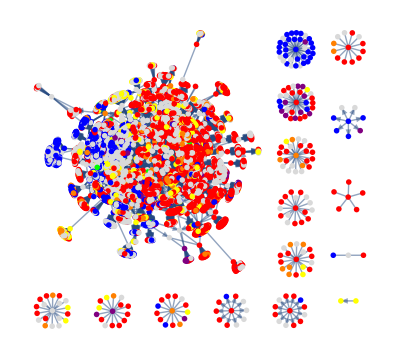

```mathematica
Show[Graph[Subgraph[g,VertexList[g],Options[g]],VertexStyle->allColors,ImageSize->Full]]
```

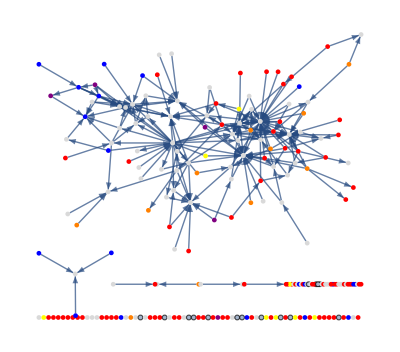

```mathematica
Show[Graph[Subgraph[g,parents,Options[g]],VertexStyle->allColors,ImageSize->Full]]
```

```mathematica
CommunityGraphPlot[prunedCC,FindGraphCommunities[prunedCC],VertexStyle->allColors,ImageSize->Full]
```

-Graphics-

Join::heads: Heads List and AdjacencyList at positions 1 and 2 are expected to be the same.

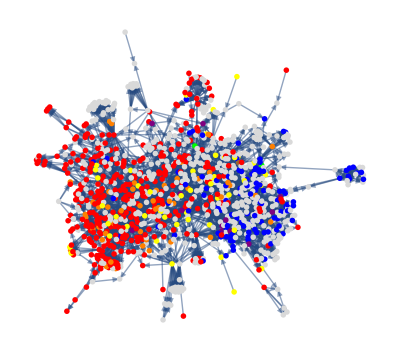

```mathematica
toHighlight = {1};
HighlightGraph[prunedCC,NeighborhoodGraph[prunedCC,1],VertexStyle->allColors,ImageSize->Full,GraphHighlightStyle->"DehighlightFade"]
```

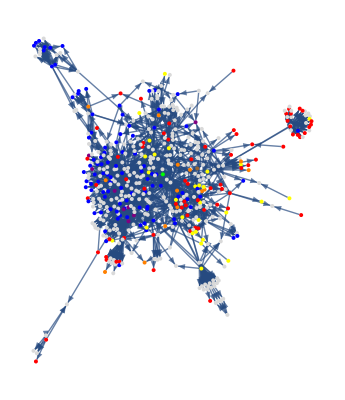

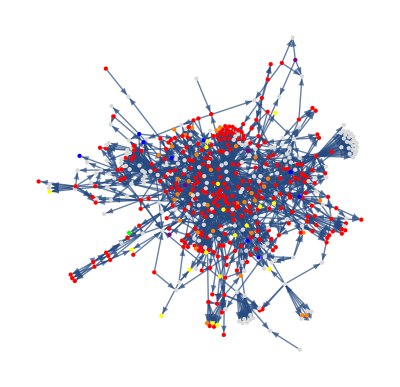

```mathematica
side1 =  Subgraph[g,partition[[1]],Options[g],VertexStyle->allColors,ImageSize->Full];
Show[side1]
side2 =  Subgraph[g,partition[[2]],Options[g],VertexStyle->allColors,ImageSize->Full];
Show[side2]
```

```mathematica
layout ={"SpringElectricalEmbedding","RepulsiveForcePower"->-2.5};
labels = Table[vertices[[i]]->Placed[Pane[Style[PropertyValue[{g,vertices[[i]]},"title"],LineSpacing->{1,0}],250,FrameMargins->None,ImageSize->Small,ImageSizeAction->"ShrinkToFit"],Center],{i,1,Length[vertices]}];
```

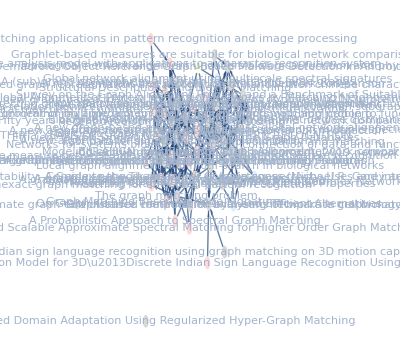

```mathematica
toRead =Graph[Subgraph[g, vertices, Options[g]],VertexLabels->labels,VertexStyle->toReadColors,GraphLayout->layout,EdgeStyle->Arrowheads[Medium],VertexSize->{"Nearest",0.8},ImageSize->Full,AspectRatio->0.9];
Show[toRead]
```

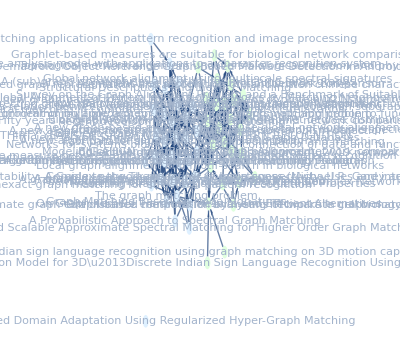

```mathematica
colorlabels = {};
For[i=1,i≤Length[vertices],i++,
If[MemberQ[partition[[1]],vertices[[i]]],AppendTo[colorlabels,vertices[[i]]->Directive[LightGreen,EdgeForm[None]]]];
If[MemberQ[partition[[2]],vertices[[i]]],AppendTo[colorlabels,vertices[[i]]->Directive[LightBlue,EdgeForm[None]]]];]

toRead =Graph[Subgraph[g, vertices, Options[g]],GraphLayout->{"SpringElectricalEmbedding","RepulsiveForcePower"->-2.5},VertexStyle->colorlabels,EdgeStyle->Arrowheads[Medium],VertexSize->{"Nearest",0.8},VertexLabels->Table[vertices[[i]]->Placed[Pane[Style[PropertyValue[{g,vertices[[i]]},"title"],LineSpacing->{1,0}],250,FrameMargins->None,ImageSize->Small,ImageSizeAction->"ShrinkToFit"],Center],{i,1,Length[vertices]}],AspectRatio->0.9, ImageSize->Full];
Show[toRead]
```

```mathematica
gridlist = {{"Vert #", "Subject","Nbhd", "Side 1", "Side 2", "title"}};
For[i=1,i≤Length[vertices],i++,
nbhd = NeighborhoodGraph[gsub,vertices[[i]]];
verts = VertexList[nbhd];
title = PropertyValue[{g,vertices[[i]]},"title"];
AppendTo[gridlist,{vertices[[i]],PropertyValue[{g,vertices[[i]]},"subject"],Length[verts],Length[Intersection[verts,partition[[1]]]],Length[Intersection[verts, partition[[2]]]], title}]
]
Grid[gridlist,Alignment->Left]
```

Vert # | Subject | Nbhd | Side 1 | Side 2 | title
1 | 0 | 22 | 15 | 7 | Fifty years of graph matching, network alignment and network comparison
5 | 0 | 15 | 10 | 5 | Networks for systems biology: conceptual connection of data and function
7 | 2 | 7 | 7 | 0 | Global network alignment using multiscale spectral signatures
10 | 0 | 13 | 1 | 12 | Error correcting graph matching: on the influence of the underlying cost function
14 | 0 | 10 | 10 | 0 | MAGNA: Maximizing Accuracy in Global Network Alignment
28 | 0 | 4 | 4 | 0 | Graphlet-based measures are suitable for biological network comparison
39 | 0 | 7 | 6 | 1 | On Graph Kernels: Hardness Results and Efficient Alternatives
44 | 2 | 8 | 8 | 0 | Pairwise Alignment of Protein Interaction Networks
46 | 0 | 6 | 6 | 0 | Alignment-free protein interaction network comparison
50 | 2 | 7 | 7 | 0 | Biological network comparison using graphlet degree distribution
54 | 0 | 10 | 10 | 0 | NETAL: a new graph-based method for global alignment of protein\u2013protein interaction networks
55 | 13 | 10 | 4 | 6 | Computers and Intractability: A Guide to the Theory of NP-Completeness (Michael R. Garey and David S. Johnson)
58 | 0 | 16 | 1 | 15 | Recent developments in graph matching
78 | 0 | 10 | 10 | 0 | Modeling cellular machinery through biological network comparison
97 | 1 | 7 | 2 | 5 | A graph distance metric based on the maximal common subgraph
98 | 0 | 24 | 1 | 23 | THIRTY YEARS OF GRAPH MATCHING IN PATTERN RECOGNITION
103 | 0 | 6 | 6 | 0 | Collective dynamics of \u2018small-world\u2019 networks
104 | 0 | 13 | 11 | 2 | A new graph-based method for pairwise global network alignment
105 | 0 | 12 | 4 | 8 | An Algorithm for Subgraph Isomorphism
109 | 1 | 8 | 2 | 6 | On a relation between graph edit distance and maximum common subgraph
117 | 0 | 7 | 7 | 0 | Topological network alignment uncovers biological function and phylogeny
123 | 1 | 7 | 0 | 7 | A linear programming approach for the weighted graph matching problem
128 | 0 | 10 | 0 | 10 | An eigendecomposition approach to weighted graph matching problems
193 | 1 | 8 | 0 | 8 | A graduated assignment algorithm for graph matching
262 | 0 | 9 | 0 | 9 | A new algorithm for subgraph optimal isomorphism
315 | 1 | 9 | 0 | 9 | A distance measure between attributed relational graphs for pattern recognition
317 | 1 | 5 | 0 | 5 | Inexact graph matching for structural pattern recognition
318 | 1 | 6 | 2 | 4 | A new algorithm for error-tolerant subgraph isomorphism detection
326 | 1 | 6 | 0 | 6 | Structural Descriptions and Inexact Matching
349 | 1 | 6 | 0 | 6 | A shape analysis model with applications to a character recognition system
365 | 1 | 9 | 0 | 9 | A graph distance measure for image analysis
368 | 1 | 8 | 0 | 8 | Structural matching in computer vision using probabilistic relaxation
369 | 1 | 6 | 0 | 6 | Hierarchical attributed graph representation and recognition of handwritten chinese characters
611 | 1 | 4 | 0 | 4 | Linear time algorithm for isomorphism of planar graphs (Preliminary Report)
745 | 12 | 6 | 5 | 1 | Pairwise Global Alignment of Protein Interaction Networks by Matching Neighborhood Topology
755 | 0 | 6 | 6 | 0 | Conserved patterns of protein interaction in multiple species
857 | 0 | 5 | 0 | 5 | Approximate graph edit distance computation by means of bipartite graph matching
861 | 0 | 8 | 4 | 4 | Local graph alignment and motif search in biological networks
888 | 0 | 6 | 6 | 0 | Network Motifs: Simple Building Blocks of Complex Networks
1199 | 0 | 8 | 1 | 7 | The Hungarian method for the assignment problem
1310 | 1 | 9 | 0 | 9 | Graph Matching Based on Node Signatures
1320 | 0 | 7 | 0 | 7 | Exact and approximate graph matching using random walks
1416 | 0 | 6 | 6 | 0 | Global alignment of multiple protein interaction networks with application to functional orthology detection
2015 | 0 | 10 | 9 | 1 | Fast parallel algorithms for graph similarity and matching
2140 | 1 | 9 | 0 | 9 | Fast computation of Bipartite graph matching
2432 | 1 | 4 | 0 | 4 | Fast and Scalable Approximate Spectral Matching for Higher Order Graph Matching
2577 | 1 | 4 | 0 | 4 | A Probabilistic Approach to Spectral Graph Matching
2593 | 1 | 3 | 0 | 3 | Graph matching applications in pattern recognition and image processing
2631 | 0 | 10 | 1 | 9 | The graph matching problem
3025 | 2 | 4 | 4 | 0 | Graph-based methods for analysing networks in cell biology
3158 | 1 | 10 | 4 | 6 | BIG-ALIGN: Fast Bipartite Graph Alignment
3181 | 0 | 7 | 0 | 7 | A (sub)graph isomorphism algorithm for matching large graphs
3230 | 2 | 4 | 4 | 0 | Complex network measures of brain connectivity: Uses and interpretations
3398 | 1 | 7 | 0 | 7 | Efficient Graph Similarity Search Over Large Graph Databases
4094 | 3 | 4 | 3 | 1 | Demadroid: Object Reference Graph-Based Malware Detection in Android
4217 | 0 | 2 | 2 | 0 | Indian sign language recognition using graph matching on 3D motion captured signs
4655 | 0 | 6 | 5 | 1 | Predicting Graph Categories from Structural Properties
4679 | 0 | 10 | 10 | 0 | Survey on the Graph Alignment Problem and a Benchmark of Suitable Algorithms
4962 | 13 | 12 | 0 | 12 | Efficient Graph Matching Algorithms
5345 | 1 | 2 | 2 | 0 | Early Estimation Model for 3D\u2013Discrete Indian Sign Language Recognition Using Graph Matching
5765 | 0 | 1 | 0 | 1 | Unsupervised Domain Adaptation Using Regularized Hyper-Graph Matching

```mathematica
nb1 = VertexList[NeighborhoodGraph[gsub,1]]
nb2 = VertexList[NeighborhoodGraph[gsub,2631]]
both = Intersection[nb1,nb2]
For[i=1,i≤Length[both],i++,
Print[PropertyValue[{g,both[[i]]},"title"]]]
```

{1,5,7,10,14,28,39,44,46,50,54,55,58,78,97,98,103,104,105,109,117,4094}

{2631,39,55,97,98,315,317,365,611,857}

{39,55,97,98}

On Graph Kernels: Hardness Results and Efficient Alternatives

Computers and Intractability: A Guide to the Theory of NP-Completeness (Michael R. Garey and David S. Johnson)

A graph distance metric based on the maximal common subgraph

THIRTY YEARS OF GRAPH MATCHING IN PATTERN RECOGNITION

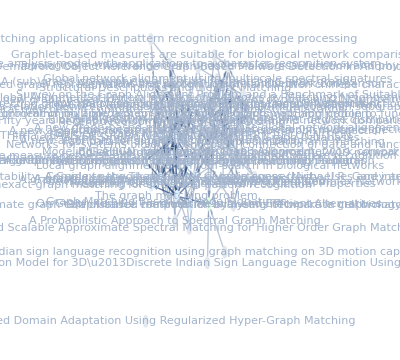

```mathematica
vert = 2631;gsub = Subgraph[g,vertices,VertexLabels->labels,GraphLayout->{"SpringElectricalEmbedding","RepulsiveForcePower"->-2.5},EdgeStyle->Arrowheads[Medium],VertexStyle->EdgeForm[None],VertexSize->{"Nearest",0.8}];
Show[HighlightGraph[toRead,NeighborhoodGraph[gsub,vert],GraphHighlightStyle->"DehighlightFade",VertexStyle->colorlabels,ImageSize->Full,AspectRatio->0.9]]
```